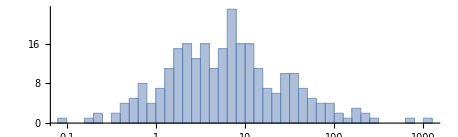

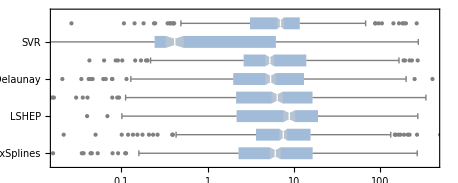

```mathematica
(* Generate histogram for Forest Fire data *)
raw=Import["/Users/thomaslux/Git/VarSys/Paper_[2019-02]_Numerical_Algorithms/Data/Results/data_forestfires_area.csv"][[All,1]];
ratio=.3;
Histogram[{{},raw},{"Log",50},PlotRange->Automatic,AspectRatio->ratio,LabelStyle->{FontSize->12,FontFamily->"Liberation Serif",FontColor->Black}]

ratio=.4;
results=Import["/Users/thomaslux/Git/VarSys/Paper_[2019-02]_Numerical_Algorithms/Data/Results/absolute_error_results_forestfires.csv"];
BoxWhiskerChart[{Reverse[results[[2;;-1,2;;-1]]]},{{"MedianNotch"},{"Outliers",Automatic,Gray}},BarOrigin->Left,
ScalingFunctions->"Log", PlotRange->{{-4,6},All},ChartStyle->ColorData["Aquamarine"],PlotRangeClipping->True,
AspectRatio->ratio,ChartLabels->Reverse[results[[2;;-1,1]]],LabelStyle->{FontSize->12,FontFamily->"Liberation Serif",FontColor->Black}]
```

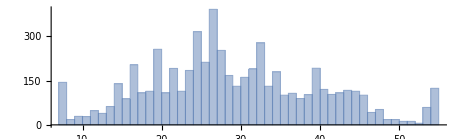

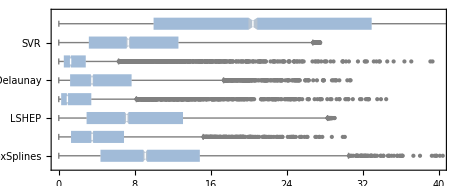

```mathematica
(* Generate histogram for Parkinsons data *)
raw=Import["/Users/thomaslux/Git/VarSys/Paper_[2019-02]_Numerical_Algorithms/Data/Results/data_parkinsons_updrs_total_UPDRS.csv"][[All,1]];
ratio=.3;
Histogram[{{},raw},50,PlotRange->Automatic,AspectRatio->ratio,LabelStyle->{FontSize->12,FontFamily->"Liberation Serif",FontColor->Black}]

ratio=.4;
results=Import["/Users/thomaslux/Git/VarSys/Paper_[2019-02]_Numerical_Algorithms/Data/Results/absolute_error_results_parkinsons_updrs.csv"];
BoxWhiskerChart[{Reverse[results[[2;;-1,2;;-1]]]},{{"MedianNotch"},{"Outliers",Automatic,Gray}},BarOrigin->Left,
 PlotRange->{{0,40},All},ChartStyle->ColorData["Aquamarine"],PlotRangeClipping->True,
AspectRatio->ratio,ChartLabels->Reverse[results[[2;;-1,1]]],LabelStyle->{FontSize->12,FontFamily->"Liberation Serif",FontColor->Black}]
```

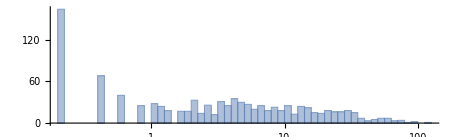

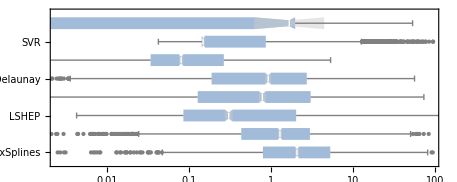

```mathematica
(* Generate histogram for Sydney, Australia Daily Rainfall data *)
raw=Import["/Users/thomaslux/Git/VarSys/Paper_[2019-02]_Numerical_Algorithms/Data/Results/data_weatherAUS_RainfallTomorrow.csv"][[All,1]];
ratio=.3;
Histogram[{{},raw},{"Log",50},PlotRange->Automatic,AspectRatio->ratio,LabelStyle->{FontSize->12,FontFamily->"Liberation Serif",FontColor->Black}]

ratio=.4;
results=Import["/Users/thomaslux/Git/VarSys/Paper_[2019-02]_Numerical_Algorithms/Data/Results/absolute_error_results_weatherAUS.csv"];
BoxWhiskerChart[{Reverse[results[[2;;-1,2;;-1]]]},{{"MedianNotch"},{"Outliers",Automatic,Gray}},BarOrigin->Left,
ScalingFunctions->"Log", PlotRange->{{-6,4.5},All},ChartStyle->ColorData["Aquamarine"],PlotRangeClipping->True,
AspectRatio->ratio,ChartLabels->Reverse[results[[2;;-1,1]]],LabelStyle->{FontSize->12,FontFamily->"Liberation Serif",FontColor->Black}]
```

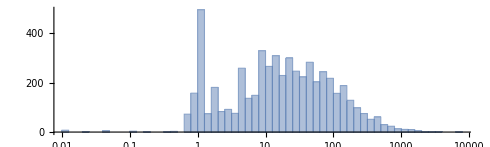

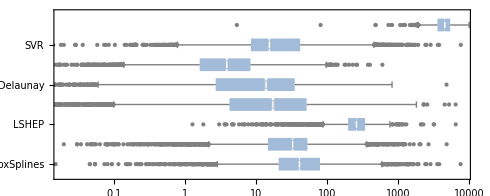

```mathematica
(* Generate histogram for Credit Card Transaction data *)
raw=Import["/Users/thomaslux/Git/VarSys/Paper_[2019-02]_Numerical_Algorithms/Data/Results/data_creditcard_Amount.csv"][[All,1]];
ratio=.3;
Histogram[{{},raw},{"Log",50},PlotRange->Automatic,AspectRatio->ratio,LabelStyle->{FontSize->12,FontFamily->"Liberation Serif",FontColor->Black}]

ratio=.4;
results=Import["/Users/thomaslux/Git/VarSys/Paper_[2019-02]_Numerical_Algorithms/Data/Results/absolute_error_results_creditcard.csv"];
BoxWhiskerChart[{Reverse[results[[2;;-1,2;;-1]]]},{{"MedianNotch"},{"Outliers",Automatic,Gray}},BarOrigin->Left,
ScalingFunctions->"Log", PlotRange->{{-4,9},All},ChartStyle->ColorData["Aquamarine"],PlotRangeClipping->True,
AspectRatio->ratio,ChartLabels->Reverse[results[[2;;-1,1]]],LabelStyle->{FontSize->12,FontFamily->"Liberation Serif",FontColor->Black}]
```

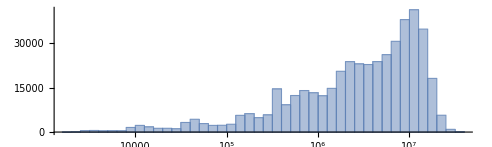

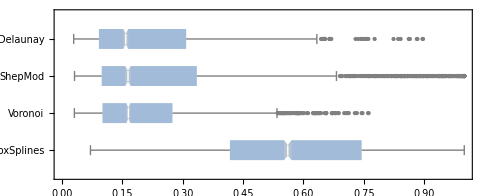

```mathematica
(* Generate histogram for I/O Zone Throughput data *)

raw=Import["/Users/thomaslux/Git/VarSys/Paper_[2019-02]_Numerical_Algorithms/Data/Results/data_iozone_150_Throughput.csv"][[All,1]];
ratio=.3;
Histogram[{{},raw},{"Log",50},PlotRange->Automatic,AspectRatio->ratio,LabelStyle->{FontSize->12,FontFamily->"Liberation Serif",FontColor->Black}]

ratio=.4;
results=Import["/Users/thomaslux/Git/VarSys/Paper_[2019-02]_Numerical_Algorithms/Data/Results/absolute_error_results_iozone_150.csv"];
BoxWhiskerChart[{Reverse[results[[2;;-1,2;;-1]]]},{{"MedianNotch"},{"Outliers",Automatic,Gray}},
 PlotRange->{{0,1},All},ChartStyle->ColorData["Aquamarine"],PlotRangeClipping->True,BarOrigin->Left,
AspectRatio->ratio,ChartLabels->Reverse[results[[2;;-1,1]]],LabelStyle->{FontSize->12,FontFamily->"Liberation Serif",FontColor->Black}]
```

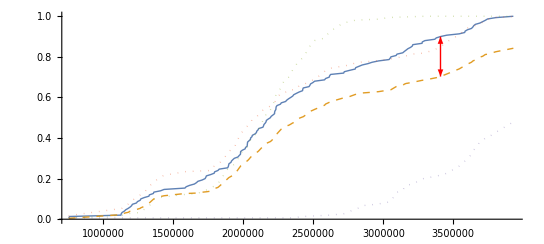

```mathematica
(* Generate Delaunay Example Prediction Plot *)
sample=Import["/Users/thomaslux/Git/VarSys/Paper_[2018-02-16]_IEEESE/Results/Delaunay_Example_Prediction.csv"];
trueConfig=sample[[1,3;;6]];
trueValues=Sort[sample[[1,7;;-1]]];
trueDist=Interpolation[Transpose[{trueValues,CDF[EmpiricalDistribution[trueValues],trueValues]}],InterpolationOrder->1];
sourceConfigs={};
sourceDists={Transpose[{trueValues,trueDist[trueValues]}]};
AppendTo[sourceDists,Transpose[{trueValues,sample[[-1,7;;-1]]}]];
For[i=2,i≤Length[sample]-1,i+=1,{
AppendTo[sourceConfigs,sample[[i,3;;6]]];
sourceValues=sample[[i,7;;-1]];
minVal=Min[sourceValues];
maxVal=Max[sourceValues];
f=Interpolation[Transpose[{sourceValues,CDF[EmpiricalDistribution[sourceValues],sourceValues]}],InterpolationOrder->1];
AppendTo[sourceDists,Transpose[{trueValues,f[Clip[trueValues,{minVal,maxVal}]]}]];
}]
opac=0.5;
ratio=.45;
aSize=.02;
Show[ListLinePlot[sourceDists,LabelStyle->{FontSize->12,FontFamily->"Liberation Serif",FontColor->Black},PlotStyle->{Thick,{Thick,Dashed},{Thick,Dotted,Opacity[opac]},{Thick,Dotted,Opacity[opac]},{Thick,Dotted,Opacity[opac]}},AspectRatio->ratio],Graphics[{Red,Thick,Arrowheads[{-aSize,aSize}],Arrow[{{3408768.28,0.70306},{3408768,0.89933}}]}]]
```

Shape of subdata: {3016}

Min and Max:      0.0703461  1.

Shape of subdata: {3016}

Min and Max:      0.0286901  0.897434

Shape of subdata: {3016}

Min and Max:      0.0307091  1.

Shape of subdata: {3016}

Min and Max:      0.0303205  0.762108

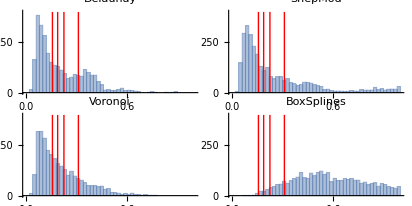

```mathematica
(* Distribution of performance by algorithm *)
(* KS Stats to P Values (for comparing two sets of 150 samples) *)
(*   0.1568      0.05    *)
(*   0.1879      0.01    *)
(*   0.2251      0.001   *)
(*   0.3110      1.0e-6  *)
(* Functions for extracting rows from data based on values in certain columns *)
data=Import["/Users/thomaslux/Git/VarSys/Paper_[2019-02]_Numerical_Algorithms/Data/Results/absolute_error_results_iozone_150.csv"];
colNames=data[[1]];
algCol=Position[colNames,"Algorithm"][[1,1]];
algNames=Union[data[[All,algCol]]][[2;;-1]];
ksValues={0.1568,0.1879,0.2251,0.3110};
dataByVal[col_,vals_,d_:data]:={
select[row_]:=Length[Position[vals,row[[col]]]]>0;
Select[d,select]
}[[1]][[1,2;;-1]];
dataByAlg[alg_,d_:data]:=dataByVal[algCol,{alg},d];

plots={};
ratio=0.5;
For[i=1,i≤Length[algNames],i+=1,{
subdata=dataByAlg[algNames[[i]]];
Print["Shape of subdata: ",Dimensions[subdata]];
Print["Min and Max:      ",Min[subdata],"  ",Max[subdata]];
hist=Show[Histogram[{{},subdata},{0,1,1/50},PlotLabel->algNames[[i]],PlotRange->Automatic,AspectRatio->ratio,LabelStyle->{FontSize->12,FontFamily->"Liberation Serif",FontColor->Black}],
(*GridLines->{{{0.1568,Directive[Opacity[1.],Thick,Red]},
		{0.1879,Directive[Opacity[1.],Thick,Red]},
		{0.2251,Directive[Opacity[1.],Thick,Red]},
		{0.3110,Directive[Opacity[1.],Thick,Red]}},None}*)
Graphics[{Red,Thick,Line[{{0.1568,0},{0.1568,400}}]}],
Graphics[{Red,Thick,Line[{{0.1879,0},{0.1879,400}}]}],
Graphics[{Red,Thick,Line[{{0.2251,0},{0.2251,400}}]}],
Graphics[{Red,Thick,Line[{{0.3110,0},{0.3110,400}}]}]];
AppendTo[plots,hist];
}]
GraphicsGrid[{{plots[[2]],plots[[3]]},{plots[[4]],plots[[1]]}},
Spacings->0,AspectRatio->1/GoldenRatio]
```